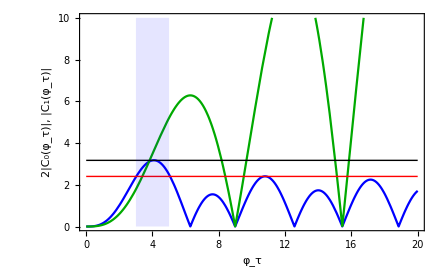

/home/tianmin/Desktop/libingyu/manuscript/demo.svg

```mathematica
Clear["Global`*"];
C0[τ_]:=Sin[τ]-4/τ Sin[τ/2]^2;
C1[τ_]:=τ Cos[τ/2]-2Sin[τ/2];
img=Module[{upper=10},
Show[{
Plot[{2Abs@C0[τ],Abs@C1[τ]},{τ,0,20},
PlotStyle->{Blue,Darker@Green},
PlotRange->{0,upper},Frame->True,
FrameLabel->{Style["φ_τ",12,FontFamily->"Times"],Style["2|C_0(φ_τ)|, |C_1(φ_τ)|",12,FontFamily->"Times"]}
],
Graphics[{
{Red,Line[{{0,2.4},{20,2.4}}]},
{Black,Line[{{0,3.17},{20,3.17}}]},
{FaceForm[Directive[Opacity[0.1],Blue]],Rectangle[{3,0},{5,upper}]}
}]
}]
]
Export["/home/tianmin/Desktop/libingyu/manuscript/demo.svg",img]
```